```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[StringDrop[NotebookDirectory[],-4]]
```

H:\2_Programming\physics\5d_flavourful_axion

```mathematica
<<"WarpFlavourAxion`"
```

### Import Data

```mathematica
quarkData = <<"output/yukawa_quark.m";
Print["Number of Yu Yd 3x3 matrix pairs"]
Dimensions[quarkData]
```

Number of Yu Yd 3x3 matrix pairs

{861,2,3,3}

```mathematica
leptonData = <<"output/yukawa_lepton.m";
Print["Number of Yn Ye 3x3 matrix pairs (normal hierarchy)"]
Dimensions[leptonData[[1]]]
Print["Number of Yn Ye 3x3 matrix pairs (inverted hierarchy)"]
Dimensions[leptonData[[2]]]
```

Number of Yn Ye 3x3 matrix pairs (normal hierarchy)

{4323,2,3,3}

Number of Yn Ye 3x3 matrix pairs (inverted hierarchy)

{3975,2,3,3}

```mathematica
quarkAData = Table[
yu = quarkData[[i, 1]]; yd = quarkData[[i,2]];myu=Minors[yu];myd=Minors[yd];
QuarkAMatrices[yu, yd, myu, myd]
,{i,Length[quarkData]}
];//AbsoluteTiming
Clear[yu,yd,myu,myd]
Dimensions[quarkAData]
```

{2.90095,Null}

{861,4,3,3}

```mathematica
leptonADataNH = Table[
yn = leptonData[[1]][[i, 1]]; ye = leptonData[[1]][[i,2]];myn=Minors[yn];mye=Minors[ye];
LeptonAMatrices[yn, ye, myn, mye,1]
,{i,Length[leptonData[[1]]]}
];//AbsoluteTiming
Clear[yn,ye,myn,mye]
Dimensions[leptonADataNH]
```

{4.53491,Null}

{4323,2,3,3}

```mathematica
leptonADataIH = Table[
yn = leptonData[[2]][[i, 1]]; ye = leptonData[[2]][[i,2]];myn=Minors[yn];mye=Minors[ye];
LeptonAMatrices[yn, ye, myn, mye,2]
,{i,Length[leptonData[[2]]]}
];//AbsoluteTiming
Clear[yn,ye,myn,mye]
Dimensions[leptonADataIH]
```

{4.19572,Null}

{3975,2,3,3}

#### Values

```mathematica
Amean = Mean[Abs[quarkAData]];
MatrixForm/@Amean
```

{(1 | 0.145424 | 0.0076116
0.145424 | 1 | 0.03453
0.00533683 | 0.03453 | 1),(1. | 0.012741 | 0.00129859
0.012741 | 1. | 0.113841
0.00199937 | 0.113841 | 1.),(1 | 0.148058 | 0.00461282
0.148058 | 1 | 0.0291851
0.0087698 | 0.0291851 | 1),(1. | 0.136949 | 0.0840789
0.136949 | 1. | 0.20083
0.0768576 | 0.20083 | 1.)}

```mathematica
AmeanLog = Log10[Mean[Abs[quarkAData]]];
MatrixForm/@AmeanLog
```

{(0 | -0.837363 | -2.11852
-0.837363 | 0 | -1.4618
-2.27272 | -1.4618 | 0),(0. | -1.8948 | -2.88653
-1.8948 | 0. | -0.943703
-2.69911 | -0.943703 | 0.),(0 | -0.829568 | -2.33603
-0.829568 | 0 | -1.53484
-2.05701 | -1.53484 | 0),(0. | -0.863441 | -1.07531
-0.863441 | 0. | -0.697171
-1.11431 | -0.697171 | 0.)}

```mathematica
Asdev = StandardDeviation[Log10[Abs[quarkAData]]];
MatrixForm/@Asdev
```

{(0. | 0.353 | 0.476532
0.353 | 0. | 0.373543
0.377697 | 0.373543 | 0.),(5.41813×10^-18 | 0.47644 | 0.609734
0.47644 | 4.01331×10^-18 | 0.520195
0.499386 | 0.520195 | 4.62874×10^-18),(0. | 0.350429 | 0.496381
0.350429 | 0. | 0.428615
0.444675 | 0.428615 | 0.),(2.84281×10^-18 | 0.385582 | 0.437635
0.385582 | 5.16902×10^-18 | 0.428503
0.406533 | 0.428503 | 4.90665×10^-18)}

```mathematica
Amean = Mean[Abs[leptonADataNH]];
MatrixForm/@Amean
```

{(1 | 0.177199 | 0.0676686
0.177199 | 1 | 0.188125
0.063495 | 0.188125 | 1),(1. | 0.0331631 | 0.0046326
0.0331631 | 1. | 0.117935
0.00440645 | 0.117935 | 1.)}

```mathematica
AmeanLog = Log10[Mean[Abs[leptonADataNH]]];
MatrixForm/@AmeanLog
```

{(0 | -0.751539 | -1.16961
-0.751539 | 0 | -0.725555
-1.19726 | -0.725555 | 0),(0. | -1.47935 | -2.33417
-1.47935 | 0. | -0.928357
-2.35591 | -0.928357 | 0.)}

```mathematica
Asdev = StandardDeviation[Log10[Abs[leptonADataNH]]];
MatrixForm/@Asdev
```

{(0. | 0.395151 | 0.493758
0.395151 | 0. | 0.414329
0.444876 | 0.414329 | 0.),(4.61704×10^-18 | 0.577346 | 0.643857
0.577346 | 5.10475×10^-18 | 0.508594
0.551987 | 0.508594 | 4.50118×10^-18)}

```mathematica
Amean = Mean[Abs[leptonADataIH]];
MatrixForm/@Amean
```

{(1 | 0.174546 | 0.0685047
0.174546 | 1 | 0.193025
0.063605 | 0.193025 | 1),(1. | 0.0330909 | 0.00458065
0.0330909 | 1. | 0.116986
0.00437244 | 0.116986 | 1.)}

```mathematica
AmeanLog = Log10[Mean[Abs[leptonADataIH]]];
MatrixForm/@AmeanLog
```

{(0 | -0.758089 | -1.16428
-0.758089 | 0 | -0.714387
-1.19651 | -0.714387 | 0),(0. | -1.48029 | -2.33907
-1.48029 | 0. | -0.931865
-2.35928 | -0.931865 | 0.)}

```mathematica
Asdev = StandardDeviation[Log10[Abs[leptonADataIH]]];
MatrixForm/@Asdev
```

{(0. | 0.400356 | 0.507019
0.400356 | 0. | 0.415822
0.450715 | 0.415822 | 0.),(4.3755×10^-18 | 0.570468 | 0.633421
0.570468 | 4.75304×10^-18 | 0.521264
0.545872 | 0.521264 | 4.3755×10^-18)}

#### Graphs

```mathematica
getADataAbs[data_,entry_]:=Grid[Table[Histogram[Table[data[[mat,entry]][[i,j]],{mat,1,Length[data]}]//Abs//Log10//Threshold,{"Raw",21}],{i,1,3},{j,1,3}]]
```

```mathematica
getADataArg[data_,entry_]:=Grid[Table[Histogram[Table[data[[mat,entry]][[i,j]],{mat,1,Length[data]}]//Arg,{"Raw",15}],
{i,1,3},{j,1,3}]]
```

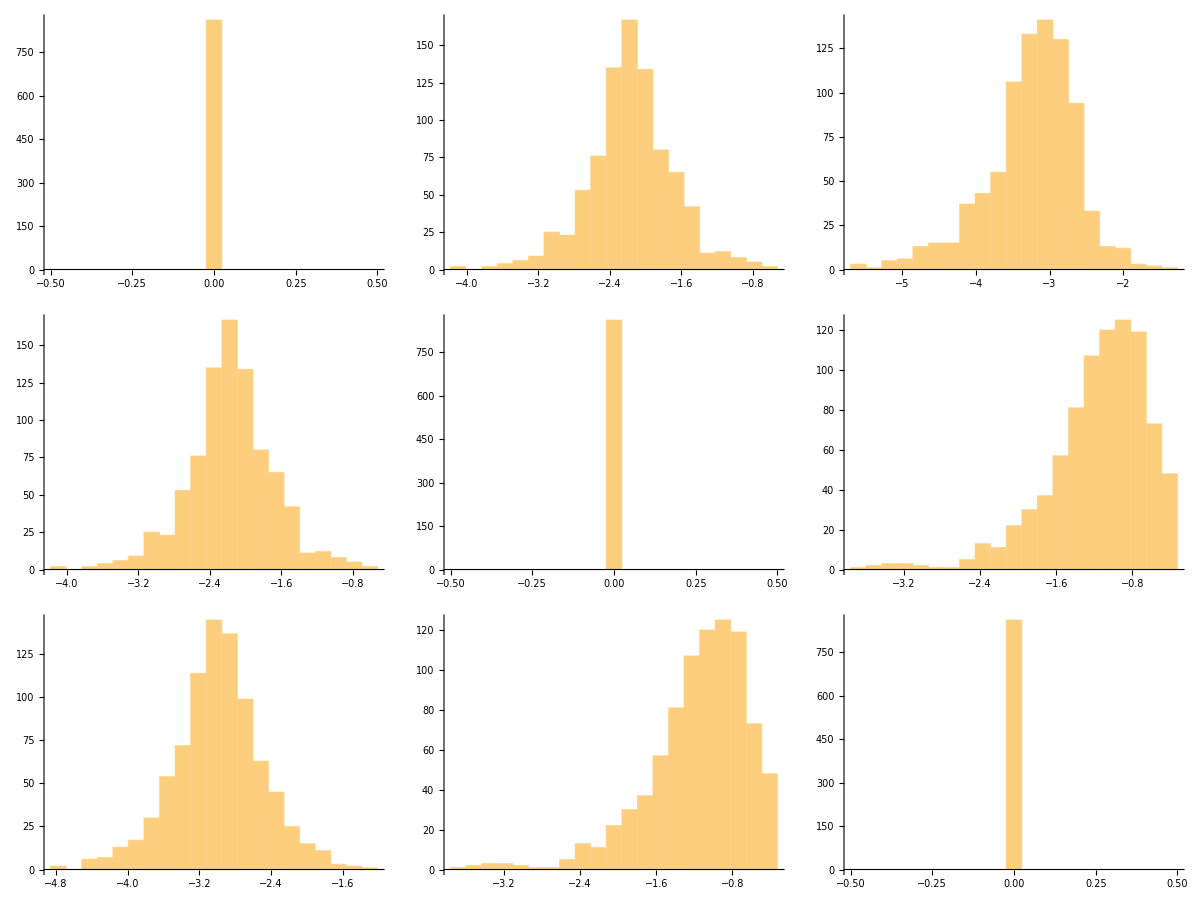

```mathematica
auR=getADataAbs[quarkAData,2]
```

```mathematica
(*  Export["Output/hist_AuR.jpg",auR] *)
```

Output/hist_AuR.jpg

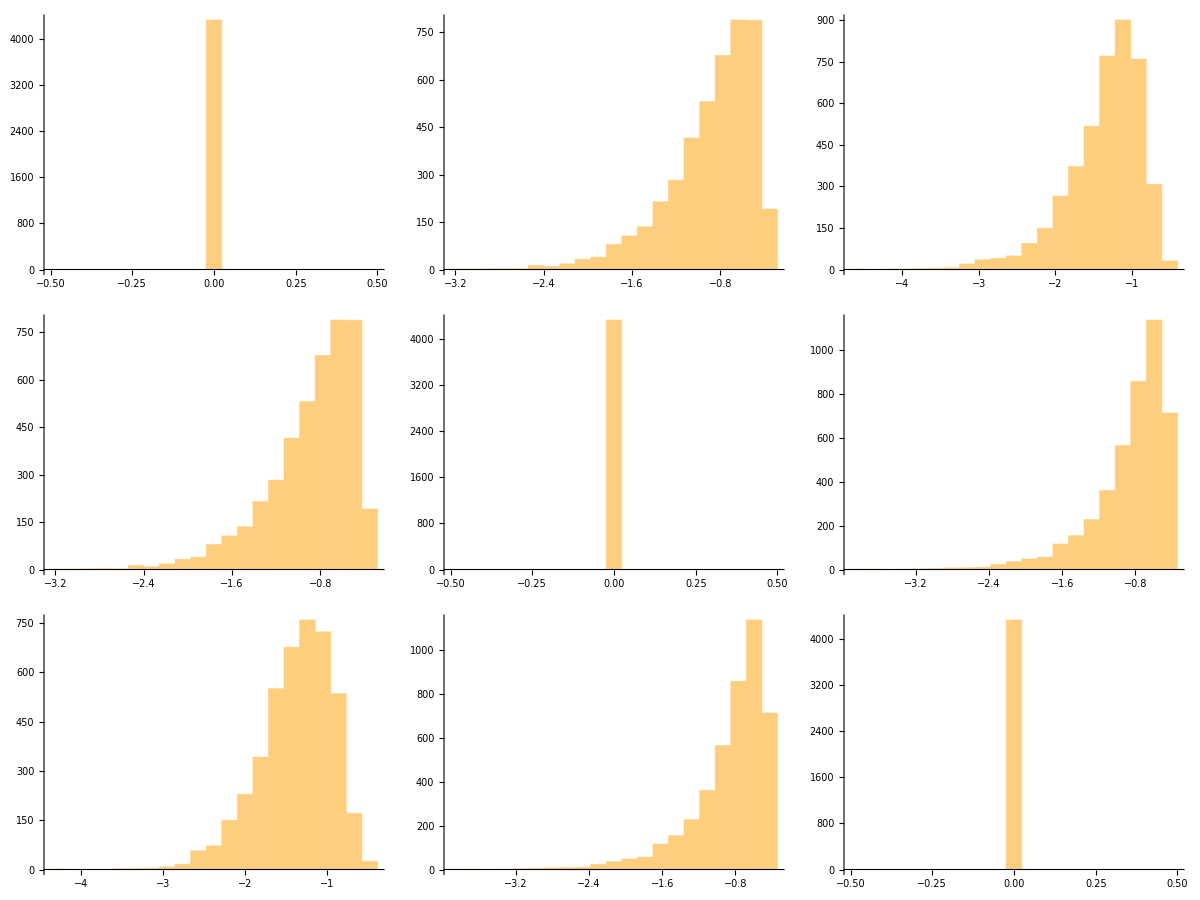

```mathematica
ael=getADataAbs[leptonADataNH,1]
```

```mathematica
(* Export["Output/hist_AeL.jpg",ael] *)
```

Output/hist_ael.jpg

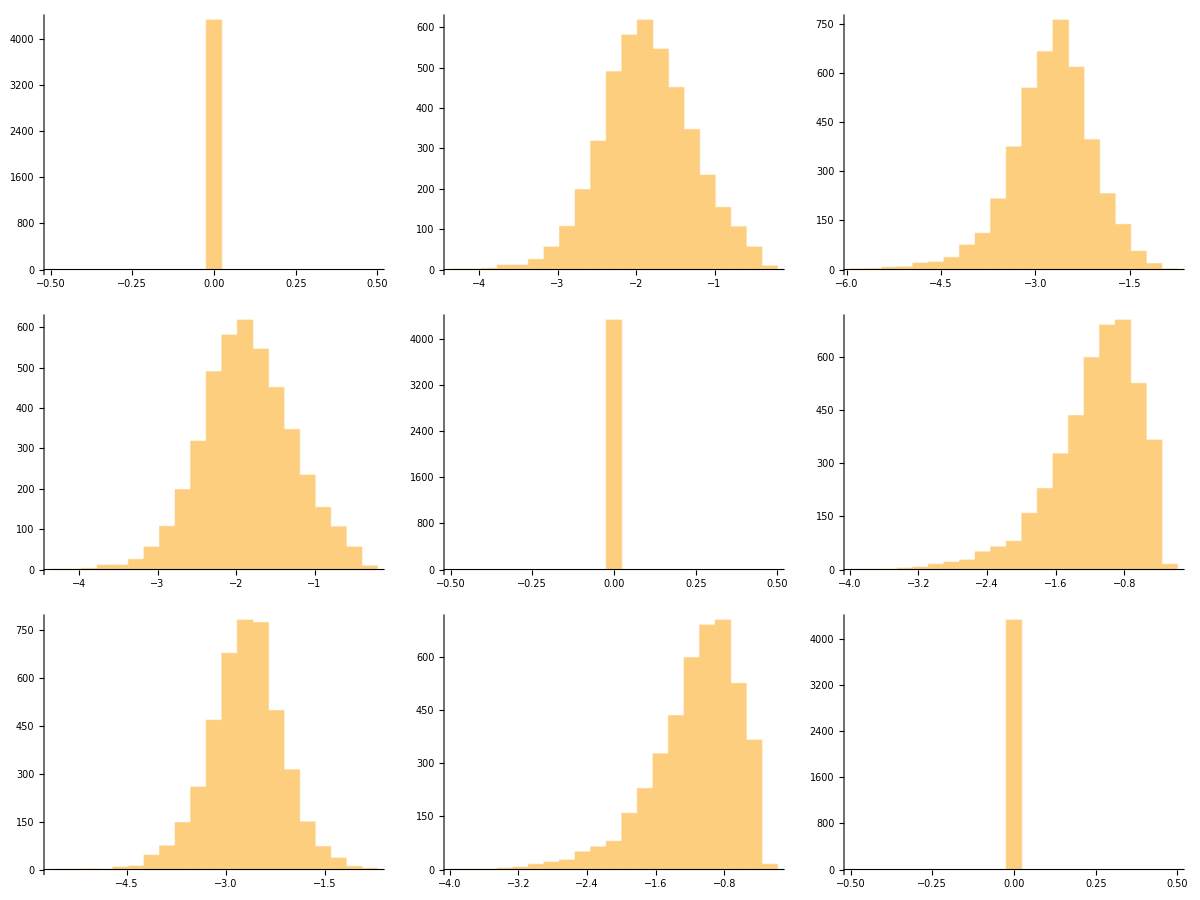

```mathematica
aeR = getADataAbs[leptonADataNH,2]
```

```mathematica
(* Export["Output/hist_AeR.jpg",aeR] *)
```

Output/hist_AeR.jpg